```mathematica
SetDirectory[NotebookDirectory[]];
<<MeshTools.wl
SolutionDirectory="solutions/";
MeshDirectory="meshes/";
```

BoundaryElementMeshJoin::shdw: Symbol BoundaryElementMeshJoin appears in multiple contexts {FEMUtils`,Global`}; definitions in context FEMUtils` may shadow or be shadowed by other definitions.

```mathematica
bmesh=BoundaryElementMeshJoin[ToBoundaryMesh[Annulus[{0,0},{1,1.5}],"BoundaryMarkerFunction"->Function[{coords,points},If[Norm[#//Mean]>1,5,6]&/@coords]],ToBoundaryMesh[Rectangle[{-3,-3},{3,3}]]];
air={{0,0},{0,2}};
dielectric={0,1.25};
mesh=ToElementMeshDefault[bmesh,Append[{#,1}&/@air,{dielectric,2}]];
```

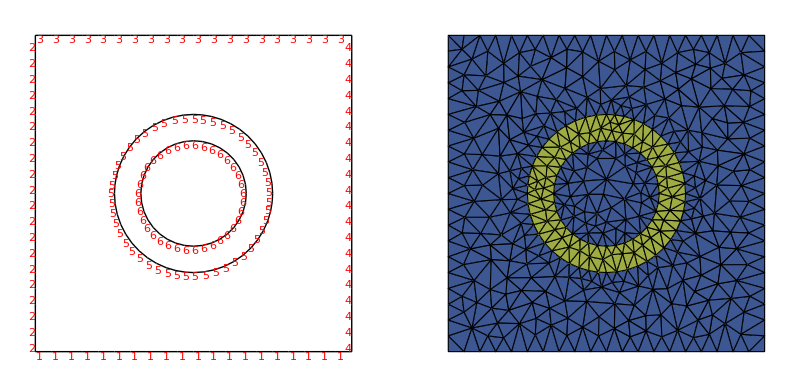

```mathematica
MeshInspect[mesh]
```

```mathematica
InterpAndShow[Import[SolutionDirectory<>"annulus_dielectric.txt","Data"],Annulus[{0,0},{1,1.5}]]
```

-Graphics-

```mathematica
mesh=ReadMesh[MeshDirectory<>"cylinder-in-square.tmh"]
```

ElementMesh[{{-3.,3.},{-3.,3.}},{TriangleElement[<908>]}]

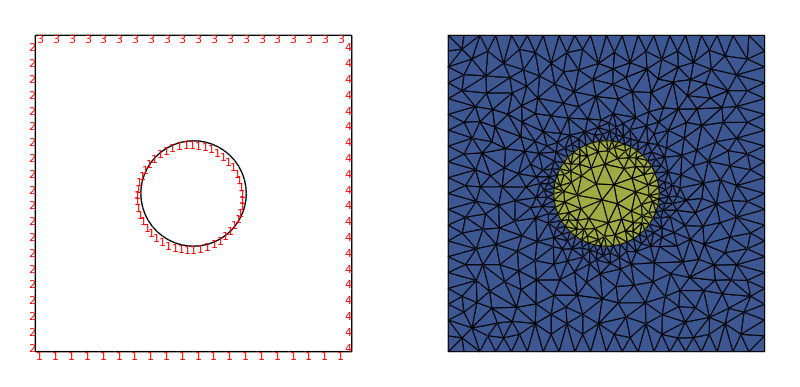

```mathematica
mesh//MeshInspect
```

```mathematica
(*Magnetized Rod*)
```

```mathematica
A=NDSolveValue[{a[x,y]{x,y}==Piecewise[{{y^2/(√(x^2+y^2)),x^2+y^2≤1}},0],DirichletCondition[a[x,y]==y^2/(2 (x^2+y^2)),x^2+y^2>2]},a,{x,y}∈mesh]
```

InterpolatingFunction[…]

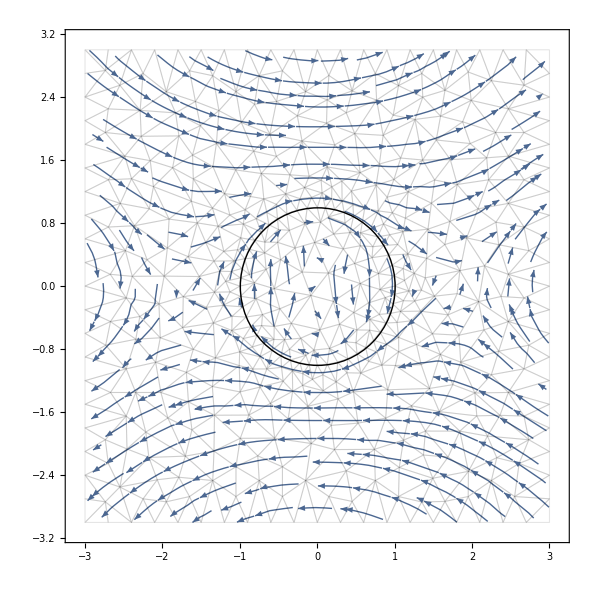

```mathematica
Show[StreamPlot[Evaluate[({0,0,A[x,y]}{x,y,z})⟦1;;2⟧],{x,y}∈mesh],Graphics[{FaceForm[None],EdgeForm[{Thin,Opacity[.1]}],DiscretizeGraphics[mesh["Wireframe"]],Circle[]}]]
```

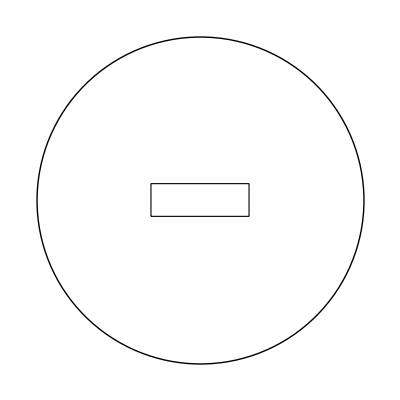

```mathematica
Graphics[{EdgeForm[],FaceForm[None],Rectangle[{-3,-1},{3,1}],Circle[{0,0},10]}]
```

```mathematica
bmesh=BoundaryElementMeshJoin[ToBoundaryMesh[Rectangle[{-3,-1},{3,1}]],ToBoundaryMesh[Circle[{0,0},10]]]
```

ElementMesh[{{-10.,10.},{-10.,10.}},Automatic]

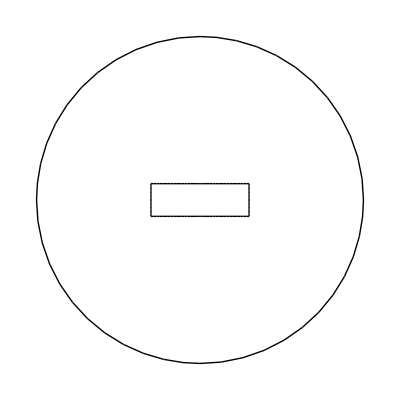

```mathematica
bmesh["Wireframe"]
```

```mathematica
mesh=ToElementMeshDefault[bmesh,{{{0,0},2},{{2,2},1}}]
```

ElementMesh[{{-10.,10.},{-10.,10.}},{TriangleElement[<1274>]}]

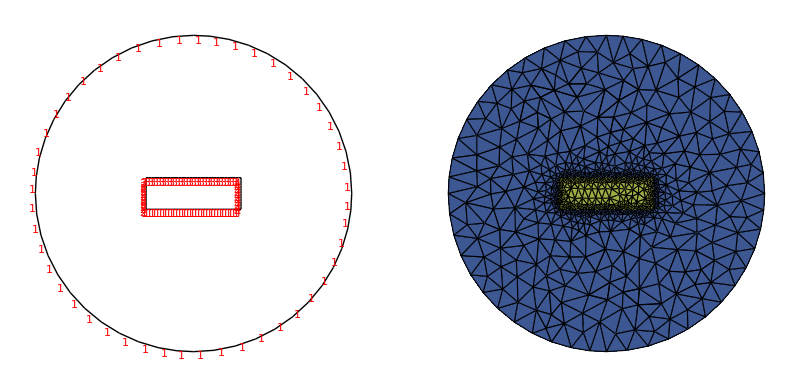

```mathematica
MeshInspect[mesh]
```

```mathematica
pde=Laplacian[a[x,y],{x,y}]==Piecewise[{{Cos[Pi(y+1)/2],{x,y}∈Rectangle[{-3,-1},{3,1}]}},0];
bcs=DirichletCondition[a[x,y]==Log[x^2+y^2]/2,x^2+y^2≥100];
```

```mathematica
A=NDSolveValue[{pde,bcs},a,{x,y}∈mesh]
```

InterpolatingFunction[…]

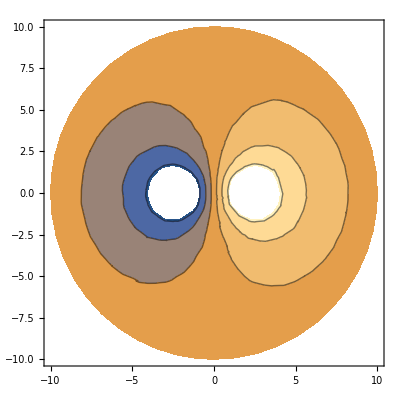

```mathematica
ContourPlot[A[x,y],{x,y}∈mesh]
```

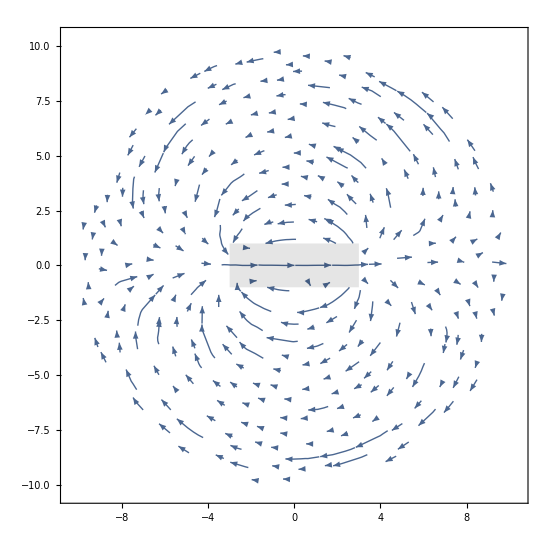

```mathematica
Show[StreamPlot[Evaluate[-Curl[A[x,y],{x,y}]],{x,y}∈mesh],Graphics[{Opacity[.1],Rectangle[{-3,-1},{3,1}]}]]
```

```mathematica
TransformedField["Polar"->"Cartesian",20/(3)(r-1)-1,{r,t}->{x,y}]
```

1/3 (-23+20 √(x^2+y^2))

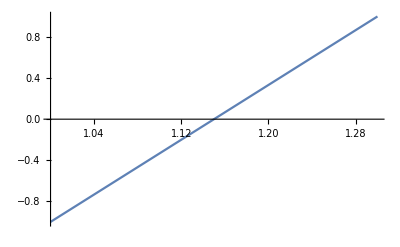

```mathematica
Plot[(2 (r-1))/(.3)-1,{r,1,1.3}]
```

```mathematica
Color
```

```mathematica
mesh
```

mesh

```mathematica
Show[DensityPlot[Cos[3ArcTan[x,y]],{x,y}∈Annulus[{0,0},{1,1.3}],ColorFunction->"RedBlueTones",PlotLegends->Automatic],Graphics[{FaceForm[None],EdgeForm[Black],Table[Rotate[Annulus[{0,0},{1,1.3},{Pi/3+.01,2Pi/3-.01}],x,{0,0}],{x,-Pi/3,2*Pi,Pi/3}],FaceForm[White],Table[Rotate[Annulus[{0,0},{1,1.3},{-.01,+.01}],x,{0,0}],{x,-Pi/3,2*Pi,Pi/3}]}]]
```

-Graphics-

```mathematica
Color
```

```mathematica
Graphics[Table[Rotate[Annulus[{0,0},{1,1.3},{Pi/3+.01,2Pi/3-.01}],x,{0,0}],{x,-Pi/3,2*Pi,Pi/3}]]
```

EmptyRegion[2]

```mathematica
?SquareWave
```

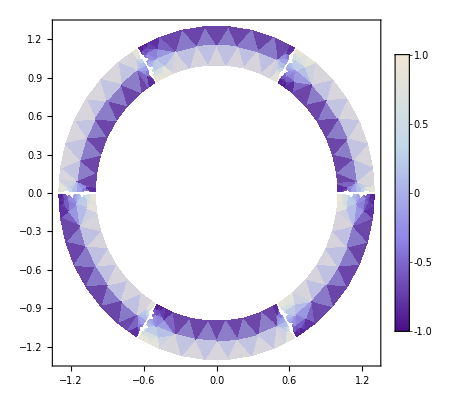

```mathematica
DensityPlot[1/3 (-23+20 √(x^2+y^2))SquareWave[ArcTan[x,y]/(2π/3)],{x,y}∈Annulus[{0,0},{1,1.3}],PlotLegends->Automatic,ColorFunction->"FushiaTones"]
```

```mathematica
Curl[{m_□[x,y],Subscript[m, y][x,y]},{x,y}]
```

```mathematica
-Derivative[0,1][Subscript[m, x]][x,y]+Derivative[1,0][Subscript[m, y]][x,y]==Cos[10/3 π (-1+√(x^2+y^2))] SquareWave[ArcTan[x,y]/(2π/3)]
```

```mathematica
NDSolve[-Derivative[0,1][Subscript[m, x]][x,y]+Derivative[1,0][Subscript[m, y]][x,y]==Cos[10/3 π (-1+√(x^2+y^2))] SquareWave[(3 ArcTan[x,y])/(2 π)],{Subscript[m, x] Subscript[m, y]},{x,y}∈mesh]
```

NDSolve::femnr: {x,y}∈mesh is not a valid region specification.

NDSolve[-m_x^(0,1)[x,y]+m_y^(1,0)[x,y]==Cos[10/3 π (-1+√(x^2+y^2))] SquareWave[(3 ArcTan[x,y])/(2 π)],{m_x m_y},{x,y}∈mesh]

```mathematica
bmesh=BoundaryElementMeshJoin[ToBoundaryMesh[Disk[{0,0},5]],ToBoundaryMesh[Annulus[{0,0},{1,1.3}]]]
```

ElementMesh[{{-5.,5.},{-5.,5.}},Automatic]

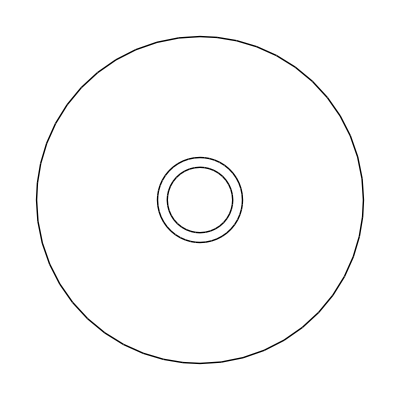

```mathematica
bmesh["Wireframe"]
```

```mathematica
mesh=ToElementMesh[bmesh,"RegionMarker"->{{{0,0},1},{{0,4},1},{{0,1.2},3}}]
```

ElementMesh[{{-5.,5.},{-5.,5.}},{TriangleElement[<912>]}]

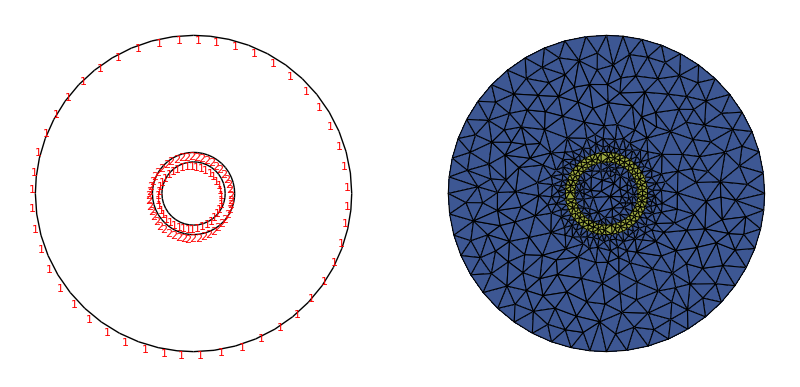

```mathematica
MeshInspect[mesh]
```

```mathematica
pde=Inactive[Div][Inactive[Dot][IdentityMatrix[2]*Piecewise[{{2,ElementMarker==3}},1],Inactive[Grad][a[x,y],{x,y}]],{x,y}]==Piecewise[{{1/3 (-23+20 √(x^2+y^2))SquareWave[ArcTan[x,y]/(2π/3)],ElementMarker==3}},0]
```

({{Piecewise[{{2, ElementMarker==3}, {1, True}}],0},{0,Piecewise[{{2, ElementMarker==3}, {1, True}}]}}.a[x,y]{x,y}Inactive){x,y}Inactive==(Piecewise[{{1/3 (-23+20 √(x^2+y^2)) SquareWave[(3 ArcTan[x,y])/(2 π)], ElementMarker==3}, {0, True}}])

```mathematica
pde
```

a^(0,2)[x,y]+a^(2,0)[x,y]==0

```mathematica
bcs=DirichletCondition[a[x,y]==0,x^2+y^2≥20];
```

```mathematica
bcs
```

DirichletCondition[a[x,y]==0,x^2+y^2≥20]

```mathematica
A=NDSolveValue[{pde,bcs},a,{x,y}∈mesh]
```

InterpolatingFunction[…]

```mathematica
Show[StreamPlot[Curl[A[x,y],{x,y}]//Evaluate,{x,y}∈mesh,StreamScale->Tiny,StreamPoints->Fine],Graphics[{FaceForm[None],EdgeForm[Black],Annulus[{0,0},{1,1.3}]}]]
```

-Graphics-

```mathematica
μAir=4 π*10^-7;
HField={10,25,50,75,108,137,160,180,200,235,285,320,365,480,560,660,800,1000,1150,1550,1840,2250,2800,3450,4350,5500,7707,11863,15839,21076,27281,35289,45642,59046,76413,98907,128000,134764,141880,149364,157235};
BField={0.0025,0.0066,0.0151,0.0264,0.05,0.1,0.15,0.2,0.25,0.35,0.5,0.6,0.7,0.9,1.,1.1,1.2,1.3,1.354,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.81,1.89,1.945,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.36,2.37,2.38,2.39};
BHData=Transpose[{BField,BField/HField}];
```

```mathematica
model=a1 Exp[-(x-b1)^2/(c1^2)]+a2/(1+Exp[(x-b2)^2/(c2^2)])^2;
fitData=FindFit[BHData,model,{a1,b1,c1,a2,b2,c2},x];
fit=Function[x,model/.fitData];
B2Norm=Sqrt[Total[Grad[a[x,y],{x,y}]^2]+$MachineEpsilon];
ν=Piecewise[{{-1/fit[B2Norm],ElementMarker==2||ElementMarker==3}},-1/μAir]*IdentityMatrix[2];
```

```mathematica
pde=Inactive[Div][Inactive[Dot][ν,Inactive[Grad][a[x,y],{x,y}]],{x,y}]==Piecewise[{{x,{x,y}∈Rectangle[{-3,-1},{3,1}]}},0];
bcs=DirichletCondition[a[x,y]==Log[x^2+y^2]/2,x^2+y^2≥100];
```